```mathematica
Clear["@"];
```

Clear::wrsym: Symbol a is Protected.

Clear::wrsym: Symbol b is Protected.

Clear::wrsym: Symbol c is Protected.

General::stop: Further output of Clear :: wrsym will be suppressed during this calculation.

```mathematica
(*<<MathSvm`;*)
Remove["W`SVM`*"]
```

```mathematica
<<SVM`;
Names["W`SVM`*"]
```

{coef0,cost,degree,IdentityKernel,KernelMatrix,kernelType,nu,PolynomialKernel,QPSolve,qpType,RBFKernel,SVMClassify,SVMLoad,SVMPlot,SVMSave,SVMTrain,svmType,t,γ}

```mathematica
Names["W`SVM`PP`*"];
```

```mathematica
?QPSolve
```

QPSolve[X_,Y_,K_,Cs_,τ_,method_] is a wrapper func for QP problem, refer to qpType for method options

```mathematica
Context[QPsolved]
```

Global`

```mathematica
W`SVM`PP`ShowWin[0]
```

0

```mathematica
(* build a set of sample*)
dim=3;
mu1=Table[i,{i,dim}];
mu2=Table[-i,{i,dim}];
sgm=DiagonalMatrix[Table[1,{i,dim}]];
s1=RandomVariate[MultinormalDistribution[mu1,sgm],10];
s2=RandomVariate[MultinormalDistribution[mu2,sgm],10];

sample=Join[s1,s2];
Dimensions[sample]

s1=RandomVariate[MultinormalDistribution[mu1,sgm],100];
s2=RandomVariate[MultinormalDistribution[mu2,sgm],100];
tests=Join[s1,s2];
ListPointPlot3D[{s1,s2},PlotStyle->{PointSize[Large]}]
```

{20,3}

-Graphics3D-

### test our SVM

```mathematica
IdentityKernel[{1,2},{10,20}]
RBFKernel[{1,2},{10,20},0.1]
```

50

2.57676×10^-18

```mathematica
IdentityKernel[sample,sample[[1]]]
IdentityKernel[sample[[2]],sample[[1]]]
```

{18.4726,14.9431,19.2161,16.5866,15.5433,16.2318,15.0858,15.4091,16.5786,15.4996,-16.6024,-13.8363,-17.5959,-16.2657,-17.2142,-14.985,-15.2764,-16.7631,-15.2265,-14.2377}

14.9431

```mathematica
K=PolynomialKernel[#1,#2,γ,degree,coef0]&/.{γ->0.1,degree->3,coef0->0};
```

```mathematica
K[sample,sample[[1]]]
```

{3.02004,2.79389,3.00949,4.03008,3.00422,1.88332,3.29583,4.0524,2.28708,1.90879,-2.07751,-2.69305,-2.23669,-2.219,-1.89158,-2.31057,-2.0305,-3.31123,-2.32566,-1.75911}

```mathematica
Dimensions[sample]
```

{20,3}

```mathematica
Attributes[IdentityKernel]={}
```

{}

```mathematica
k1=Outer[IdentityKernel,sample,sample[[{1}]],1]
```

{{17.6775},{13.7731},{16.6522},{15.9887},{16.8627},{13.3158},{16.2259},{16.4411},{15.1847},{16.0256},{-15.2924},{-15.8505},{-13.9965},{-15.5252},{-13.1532},{-14.7015},{-16.3957},{-15.4721},{-16.2009},{-17.6583}}

```mathematica
k2=Outer[IdentityKernel,sample,sample[[{1,2}]],1]
```

{{17.6775,13.7731},{13.7731,10.8446},{16.6522,13.0969},{15.9887,12.3492},{16.8627,13.3008},{13.3158,10.4431},{16.2259,12.688},{16.4411,12.9591},{15.1847,11.9533},{16.0256,12.5521},{-15.2924,-12.0938},{-15.8505,-12.579},{-13.9965,-11.0925},{-15.5252,-12.0765},{-13.1532,-10.2933},{-14.7015,-11.6625},{-16.3957,-12.9618},{-15.4721,-12.1447},{-16.2009,-12.6009},{-17.6583,-13.8836}}

```mathematica
k2[[All,1]]- k1ᵀ[[1]]
```

{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.}

```mathematica
(*k=Map[Thread[IdentityKernel[sample,#]]&,sample[[{1,2,3}]]];*)
```

```mathematica
Dimensions[k]
```

{3}

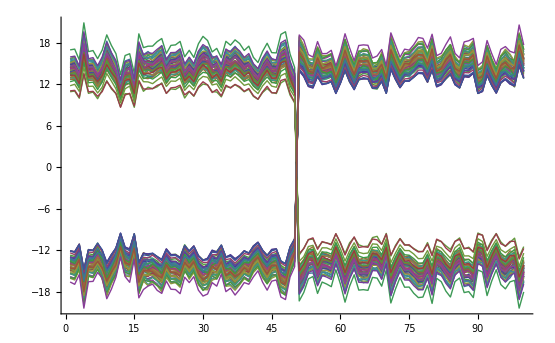

```mathematica
ListPlot[k,Joined->True]
```

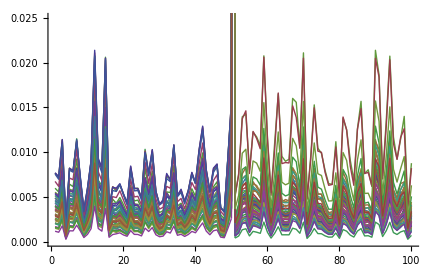

```mathematica
k=Table[RBFKernel[sample[[i]],sample[[j]]],{i,100},{j,100}];ListPlot[k,Joined->True(*,PlotRange->{0,10}*)]
```

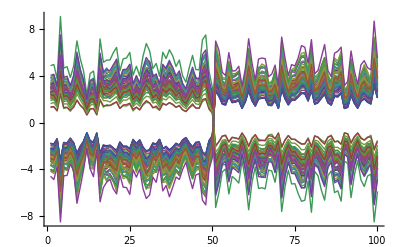

```mathematica
k=Table[PolynomialKernel[sample[[i]],sample[[j]]],{i,100},{j,100}];
ListPlot[k,Joined->True(*,PlotRange->{0,10}*)]
```

```mathematica
PolynomialKernel[{1,2},{2,3}]
```

0.512

```mathematica
ListPointPlot3D[sample]
```

-Graphics3D-

```mathematica
X=sample;
Y=Join[Table[1,{10}],Table[-1,{10}]]
```

{1,1,1,1,1,1,1,1,1,1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1}

```mathematica
a=QPSolve[X,Y,IdentityKernel,{0,∞}]
```

Compile::ctyp1: Number 0.001 in {« 1 »} is an invalid compiler variable. A symbol can be used as a valid variable.

Compile[{{{{18.4726,14.9431,19.2161,16.5866,15.5433,16.2318,15.0858,15.4091,16.5786,15.4996,16.6024,13.8363,17.5959,16.2657,17.2142,14.985,15.2764,16.7631,15.2265,14.2377},{14.9431,12.1079,15.4846,13.4945,12.5997,13.1302,12.2186,12.4294,13.4987,12.484,13.4423,11.1578,14.2504,13.1897,13.8546,12.091,12.3243,13.5811,12.3359,11.5083},{19.2161,15.4846,20.2876,17.0285,16.3171,16.9585,15.6444,16.2809,16.8476,16.5088,17.4378,14.6766,18.5549,16.8135,18.2608,15.8352,16.0791,17.4964,15.8606,15.0546},{16.5866,13.4945,17.0285,15.1923,14.0723,14.5777,13.6041,13.7067,15.2179,13.7208,14.9665,12.2992,15.8818,14.7278,15.1912,13.3444,13.5924,15.1398,13.7493,12.7623},{15.5433,12.5997,16.3171,14.0723,13.5576,13.7986,12.708,13.1995,13.8057,13.4029,14.3827,11.943,15.4139,13.7078,14.6645,12.8673,12.9792,14.3696,12.9887,12.3904},{16.2318,13.1302,16.9585,14.5777,13.7986,14.3078,13.2538,13.6299,14.4835,13.7579,14.7145,12.2688,15.6476,14.2855,15.2143,13.263,13.4778,14.8047,13.4275,12.645},{15.0858,12.2186,15.6444,13.6041,12.708,13.2538,12.3316,12.5533,13.6092,12.6112,13.5627,11.2686,14.3751,13.308,14.0008,12.2103,12.448,13.7026,12.4472,11.6151},{15.4091,12.4294,16.2809,13.7067,13.1995,13.6299,12.5533,13.0952,13.5077,13.2999,14.0787,11.8238,15.0192,13.498,14.6591,12.7448,12.9101,14.0958,12.7639,12.1599},{16.5786,13.4987,16.8476,15.2179,13.8057,14.4835,13.6092,13.5077,15.4182,13.4182,14.7209,12.0605,15.5215,14.7507,14.9772,13.1367,13.4634,14.9976,13.659,12.4907},{15.4996,12.484,16.5088,13.7208,13.4029,13.7579,12.6112,13.2999,13.4182,13.5742,14.2845,12.0427,15.2904,13.5409,14.9028,12.9495,13.074,14.2396,12.873,12.3825},{16.6024,13.4423,17.4378,14.9665,14.3827,14.7145,13.5627,14.0787,14.7209,14.2845,15.2838,12.7246,16.3486,14.6197,15.6732,13.7169,13.8611,15.2906,13.8322,13.1684},{13.8363,11.1578,14.6766,12.2992,11.943,12.2688,11.2686,11.8238,12.0605,12.0427,12.7246,10.696,13.6087,12.1112,13.2317,11.5124,11.6335,12.7045,11.4908,11.0102},{17.5959,14.2504,18.5549,15.8818,15.4139,15.6476,14.3751,15.0192,15.5215,15.2904,16.3486,13.6087,17.5485,15.4929,16.6998,14.6435,14.7474,16.2979,14.7201,14.1121},{16.2657,13.1897,16.8135,14.7278,13.7078,14.2855,13.308,13.498,14.7507,13.5409,14.6197,12.1112,15.4929,14.3744,15.0316,13.1312,13.3899,14.7828,13.4303,12.5025},{17.2142,13.8546,18.2608,15.1912,14.6645,15.2143,14.0008,14.6591,14.9772,14.9028,15.6732,13.2317,16.6998,15.0316,16.4615,14.2588,14.4591,15.6932,14.2162,13.5602},{14.985,12.091,15.8352,13.3444,12.8673,13.263,12.2103,12.7448,13.1367,12.9495,13.7169,11.5124,14.6435,13.1312,14.2588,12.4061,12.5586,13.7257,12.4251,11.8486},{15.2764,12.3243,16.0791,13.5924,12.9792,13.4778,12.448,12.9101,13.4634,13.074,13.8611,11.6335,14.7474,13.3899,14.4591,12.5586,12.7542,13.9182,12.6185,11.9506},{16.7631,13.5811,17.4964,15.1398,14.3696,14.8047,13.7026,14.0958,14.9976,14.2396,15.2906,12.7045,16.2979,14.7828,15.6932,13.7257,13.9182,15.3603,13.9182,13.1362},{15.2265,12.3359,15.8606,13.7493,12.9887,13.4275,12.4472,12.7639,13.659,12.873,13.8322,11.4908,14.7201,13.4303,14.2162,12.4251,12.6185,13.9182,12.6205,11.8718},{14.2377,11.5083,15.0546,12.7623,12.3904,12.645,11.6151,12.1599,12.4907,12.3825,13.1684,11.0102,14.1121,12.5025,13.5602,11.8486,11.9506,13.1362,11.8718,11.3795}},_Real,2},{{1,1,1,1,1,1,1,1,1,1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1},_Real,1},{0.001,_Real},{{0,∞},_Real,1}},Module[{W`SVM`PP`m$,W`SVM`PP`i$,W`SVM`PP`j$,W`SVM`PP`W$,W`SVM`PP`g$,W`SVM`PP`vars$,W`SVM`PP`sol$,W`SVM`PP`KM$,W`SVM`PP`p$},W`SVM`PP`m$=Length[{1,1,1,1,1,1,1,1,1,1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1}];W`SVM`PP`p$=Ceiling[-Log[10,0.001]];If[W`SVM`PP`p$≤0,Print[τ error];Return[]];W`SVM`PP`vars$=Table[(W`SVM`PP`α)_(W`SVM`PP`i$),{W`SVM`PP`i$,1,W`SVM`PP`m$}];W`SVM`PP`W$=∑_(W`SVM`PP`i$=1)^(W`SVM`PP`m$) (W`SVM`PP`α)_(W`SVM`PP`i$)-1/2 W`SVM`PP`vars$.{{18.4726,14.9431,19.2161,16.5866,15.5433,16.2318,15.0858,15.4091,16.5786,15.4996,16.6024,13.8363,17.5959,16.2657,17.2142,14.985,15.2764,16.7631,15.2265,14.2377},{14.9431,12.1079,15.4846,13.4945,12.5997,13.1302,12.2186,12.4294,13.4987,12.484,13.4423,11.1578,14.2504,13.1897,13.8546,12.091,12.3243,13.5811,12.3359,11.5083},{19.2161,15.4846,20.2876,17.0285,16.3171,16.9585,15.6444,16.2809,16.8476,16.5088,17.4378,14.6766,18.5549,16.8135,18.2608,15.8352,16.0791,17.4964,15.8606,15.0546},{16.5866,13.4945,17.0285,15.1923,14.0723,14.5777,13.6041,13.7067,15.2179,13.7208,14.9665,12.2992,15.8818,14.7278,15.1912,13.3444,13.5924,15.1398,13.7493,12.7623},{15.5433,12.5997,16.3171,14.0723,13.5576,13.7986,12.708,13.1995,13.8057,13.4029,14.3827,11.943,15.4139,13.7078,14.6645,12.8673,12.9792,14.3696,12.9887,12.3904},{16.2318,13.1302,16.9585,14.5777,13.7986,14.3078,13.2538,13.6299,14.4835,13.7579,14.7145,12.2688,15.6476,14.2855,15.2143,13.263,13.4778,14.8047,13.4275,12.645},{15.0858,12.2186,15.6444,13.6041,12.708,13.2538,12.3316,12.5533,13.6092,12.6112,13.5627,11.2686,14.3751,13.308,14.0008,12.2103,12.448,13.7026,12.4472,11.6151},{15.4091,12.4294,16.2809,13.7067,13.1995,13.6299,12.5533,13.0952,13.5077,13.2999,14.0787,11.8238,15.0192,13.498,14.6591,12.7448,12.9101,14.0958,12.7639,12.1599},{16.5786,13.4987,16.8476,15.2179,13.8057,14.4835,13.6092,13.5077,15.4182,13.4182,14.7209,12.0605,15.5215,14.7507,14.9772,13.1367,13.4634,14.9976,13.659,12.4907},{15.4996,12.484,16.5088,13.7208,13.4029,13.7579,12.6112,13.2999,13.4182,13.5742,14.2845,12.0427,15.2904,13.5409,14.9028,12.9495,13.074,14.2396,12.873,12.3825},{16.6024,13.4423,17.4378,14.9665,14.3827,14.7145,13.5627,14.0787,14.7209,14.2845,15.2838,12.7246,16.3486,14.6197,15.6732,13.7169,13.8611,15.2906,13.8322,13.1684},{13.8363,11.1578,14.6766,12.2992,11.943,12.2688,11.2686,11.8238,12.0605,12.0427,12.7246,10.696,13.6087,12.1112,13.2317,11.5124,11.6335,12.7045,11.4908,11.0102},{17.5959,14.2504,18.5549,15.8818,15.4139,15.6476,14.3751,15.0192,15.5215,15.2904,16.3486,13.6087,17.5485,15.4929,16.6998,14.6435,14.7474,16.2979,14.7201,14.1121},{16.2657,13.1897,16.8135,14.7278,13.7078,14.2855,13.308,13.498,14.7507,13.5409,14.6197,12.1112,15.4929,14.3744,15.0316,13.1312,13.3899,14.7828,13.4303,12.5025},{17.2142,13.8546,18.2608,15.1912,14.6645,15.2143,14.0008,14.6591,14.9772,14.9028,15.6732,13.2317,16.6998,15.0316,16.4615,14.2588,14.4591,15.6932,14.2162,13.5602},{14.985,12.091,15.8352,13.3444,12.8673,13.263,12.2103,12.7448,13.1367,12.9495,13.7169,11.5124,14.6435,13.1312,14.2588,12.4061,12.5586,13.7257,12.4251,11.8486},{15.2764,12.3243,16.0791,13.5924,12.9792,13.4778,12.448,12.9101,13.4634,13.074,13.8611,11.6335,14.7474,13.3899,14.4591,12.5586,12.7542,13.9182,12.6185,11.9506},{16.7631,13.5811,17.4964,15.1398,14.3696,14.8047,13.7026,14.0958,14.9976,14.2396,15.2906,12.7045,16.2979,14.7828,15.6932,13.7257,13.9182,15.3603,13.9182,13.1362},{15.2265,12.3359,15.8606,13.7493,12.9887,13.4275,12.4472,12.7639,13.659,12.873,13.8322,11.4908,14.7201,13.4303,14.2162,12.4251,12.6185,13.9182,12.6205,11.8718},{14.2377,11.5083,15.0546,12.7623,12.3904,12.645,11.6151,12.1599,12.4907,12.3825,13.1684,11.0102,14.1121,12.5025,13.5602,11.8486,11.9506,13.1362,11.8718,11.3795}}.W`SVM`PP`vars$;W`SVM`PP`g$=And@@Join[Table[{0,∞}⟦2⟧≥(W`SVM`PP`α)_(W`SVM`PP`i$)≥{0,∞}⟦1⟧,{W`SVM`PP`i$,1,W`SVM`PP`m$}],{∑_(W`SVM`PP`i$=1)^(W`SVM`PP`m$) {1,1,1,1,1,1,1,1,1,1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1}⟦W`SVM`PP`i$⟧ (W`SVM`PP`α)_(W`SVM`PP`i$)==0}];W`SVM`PP`sol$=NMaximize[{W`SVM`PP`W$,W`SVM`PP`g$},W`SVM`PP`vars$,Method→DifferentialEvolution,AccuracyGoal→W`SVM`PP`p$]⟦2⟧;Chop[W`SVM`PP`vars$/.W`SVM`PP`sol$,0.001]]]

```mathematica
a=QPsolve[X,Y,IdentityKernel]
```

$Aborted

```mathematica
a={-2.287132400136116*^-9,0.,0.,5.336703922945877*^-10,0.04553934229750758,0.,0.,0.,0.,0.,3.372636908540953*^-8,2.030348225894941*^-8,2.8842264141943643*^-8,2.150695910842104*^-8,3.900427799111148*^-8,3.257812901612026*^-8,0.04553904983631917,4.8136395385197635*^-8,5.2309659900572123*^-8,1.4300189511020779*^-8};
```

```mathematica
a1=Chopit[a]
```

{0,0,0,0,0.0455393,0,0,0,0,0,0,0,0,0,0,0,0.045539,0,0,0}

```mathematica
Ceiling[a1]
```

{0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0}

```mathematica
sv=Extract[sample,Position[Ceiling[a1],1]]
```

{{0.900912,1.55314,2.65981},{-0.838651,-1.71911,-2.83457}}

```mathematica
ListPointPlot3D[{sample,sv},PlotStyle->{PointSize[Medium],PointSize[Large]}]
```

-Graphics3D-

```mathematica
DisplayTogether[]
```

DisplayTogether[]

```mathematica
(* 2-class based on distance*)
```

### formal test classic SVM

```mathematica
X=sample;
Y=Join[Table[1,{10}],Table[-1,{10}]];
Dimensions[%]
```

{20}

```mathematica
Union[Y]
```

{-1,1}

```mathematica
(*m=oSVM[X,Y,IdentityKernel]*)
```

enter oSVM

aa

```mathematica
m=SVMTrain[X,Y,svmType->2,kernelType->1,qpType->2]//Timing
```

SVM train begin

{2.75387×10^-17,W`SVM`PP`svm$708}

```mathematica
MaxMemoryUsed[]
```

22220324

```mathematica
rm=m[[2]];
```

```mathematica
SVMSave[rm]
```

..\tmp\svm.mx

```mathematica
g=rm["offset"]
```

0.329838

```mathematica
rm["alpha"]
```

{0,0,0,0,0,0,0,0.0935338,0,0.021843,0,0,0,0,0,0,0,0,0.115377,0}

```mathematica
r=SVMClassify[rm,X];
```

```mathematica
HammingDistance[r[[2]],Y]
```

0

```mathematica
r[[1]]
```

{0.845527,0.894265,0.845518,0.845518,1.01184,1.03476,0.84552,0.845528,1.0032,0.845529,-1.15445,-1.15442,-1.15444,-1.22935,-1.15445,-1.15444,-1.20951,-1.15442,-1.15444,-1.18733}

```mathematica
rm["alpha"].Y
```

-1.73472×10^-18

```mathematica
SVMPlot[rm,X]
```

-Graphics3D-

```mathematica
ss=Join[s1,s2];
ssy=Join[Table[1,{100}],Table[-1,{100}]];
```

```mathematica
r=SVMClassify[rm,ss];
HammingDistance[r[[2]],ssy]
```

0

..\tmp\svm.mx

```mathematica
rm["opts"][[1]]
```

Part::partw: Part 1 of {} does not exist.

{}⟦1⟧

```mathematica
ssvm=SVMLoad[];
```

```mathematica
ssvm["opts"]
ssvm["alpha"]
```

Sequence[]

{0,0,0,0,0,0,0,0,0,0.332399,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0.0479055,0,0.284493,0,0}

```mathematica
range={{x1,Min[X[[All,1]]],Max[X[[All,1]]]},
   {x2,Min[X[[All,2]]],Max[X[[All,2]]]},
     {x3,Min[X[[All,3]]],Max[X[[All,3]]]}}
```

{{x1,-3.21996,2.31172},{x2,-3.90159,3.58359},{x3,-4.87366,4.207}}

```mathematica
f=ssvm["svi"].Map[IdentityKernel[#,{x1,x2,x3}]&,ssvm["svX"]]+ssvm["offset"];
```

```mathematica
ContourPlot3D[f==1,range[[1]],range[[2]],range[[3]]]
```

ContourPlot3D::pllim: Range specification range ⟦ 1 ⟧ is not of the form {x, xmin, xmax}.

ContourPlot3D[f==1,range⟦1⟧,range⟦2⟧,range⟦3⟧]

```mathematica
ListPointPlot3D[ssvm["svX"],PlotStyle->{Hue[0.6],PointSize[Larger]}]
```

-Graphics3D-

```mathematica
SVMPlot[ssvm,X]
```

-Graphics3D-

```mathematica
{t,degree}/.{ssvm["opts"]}
```

{t,degree}

```mathematica
g[{2,1}]
```

{4,2}

```mathematica
Total[{100}]
```

100

### Dlib qpsolve test

```mathematica
X=sample;
Y=Join[Table[1,{10}],Table[-1,{10}]];
Dimensions[%]
```

{20}

```mathematica
(*QPsolved[0.001,N[10^10],N[10^10],N[Y],Q]*)
```

{0.,0.,0.,0.0386592,0.,0.,0.0386288,0.,0.,0.,0.00232944,0.,0.,0.,0.0749585,0.,0.,0.,0.,0.}

```mathematica
qm=SVMTrain[X,Y,qpType->2,kernelType->2,t->0.0001];
```

SVM train begin

```mathematica
qm["alpha"].Y
```

0.

```mathematica
w=qm["svi"].qm["svX"];
```

```mathematica
w.Xᵀ+qm["offset"]
```

{1.0577,1.17099,1.64861,1.38171,1.66444,1.2907,1.5154,2.48998,1.,1.32119,-1.78368,-1.65408,-1.66249,-1.,-1.39815,-1.6381,-1.64721,-1.84372,-1.3209,-1.25507}

```mathematica
qm["alpha"]
```

{0,0,0,0,0,0,0,0,0.0480715,0,0,0,0,0.0480715,0,0,0,0,0,0}

```mathematica
SVMClassify[qm,X]
```

{{1.31792,2.00484,4.4176,2.53502,4.70456,2.04449,3.58564,16.3198,1.,2.19326,-4.54425,-3.6319,-3.44585,-1.,-2.11901,-3.70874,-3.34383,-4.94297,-1.88565,-1.90687},{1,1,1,1,1,1,1,1,1,1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1}}

```mathematica
SVMPlot[qm,X]
```

-Graphics3D-

```mathematica
qm["opts"]
```

Sequence[qpType→2,kernelType→1,t→0.0001]

```mathematica
X=tests;
Y=Join[Table[1,{100}],Table[-1,{100}]];
```

```mathematica
qm=SVMTrain[X,Y,qpType->2,kernelType->1,t->0.0001];
```

SVM train begin

```mathematica
qm["alpha"].Y
```

0.

```mathematica
r=SVMClassify[qm,X];
```

```mathematica
HammingDistance[r[[2]],Y]
```

0

```mathematica
SVMPlot[qm,X]
```

-Graphics3D-

```mathematica
test2=Join[RandomVariate[MultinormalDistribution[mu1,sgm],100],
RandomVariate[MultinormalDistribution[mu2,sgm],100]];
```

```mathematica
r=SVMClassify[qm,test2];
HammingDistance[r[[2]],Y]
```

0

```mathematica
SVMPlot[qm,test2]
```

-Graphics3D-

### MathSvm

```mathematica
<<MathSVM`
```

SVMClassify::shdw: Symbol "SVMClassify" appears in multiple contexts {"MathSVM`", "W`SVM`"}; definitions in context "MathSVM`" may shadow or be shadowed by other definitions.

KernelMatrix::shdw: Symbol "KernelMatrix" appears in multiple contexts {"MathSVM`", "W`SVM`"}; definitions in context "MathSVM`" may shadow or be shadowed by other definitions.

IdentityKernel::shdw: Symbol "IdentityKernel" appears in multiple contexts {"MathSVM`", "W`SVM`"}; definitions in context "MathSVM`" may shadow or be shadowed by other definitions.

RBFKernel::shdw: Symbol "RBFKernel" appears in multiple contexts {"MathSVM`", "W`SVM`"}; definitions in context "MathSVM`" may shadow or be shadowed by other definitions.

PolynomialKernel::shdw: Symbol "PolynomialKernel" appears in multiple contexts {"MathSVM`", "W`SVM`"}; definitions in context "MathSVM`" may shadow or be shadowed by other definitions.

QPSolve::shdw: Symbol "QPSolve" appears in multiple contexts {"MathSVM`", "W`SVM`"}; definitions in context "MathSVM`" may shadow or be shadowed by other definitions.

```mathematica
?QPSolve
```

QPSolve[Q,p,a,b,c,y,τ] solves the quadratic programming problem min α.Q.α+p.α, subject to a≤α≤b and y.α=c. QPSolve uses the GSMO algorithm described by Keerthi et al. τ is a solution tolerance parameter (0.01 or so is usually good enough for SVMs). Q must be a positive semidefinite matrix to guarantee convergence.

```mathematica
X=Join[sample[[;;250]],sample[[751;;]]];
(*CONSTRUCTION OF INPUT Y*)
y=Join[ConstantArray[1,250],ConstantArray[-1,250]];
Length[y]
```

500

```mathematica
KernelMatrix[IdentityKernel,X]//Dimensions
```

{500,500}

```mathematica
τ=0.01;
α=SeparableSVM[X,y,τ];
```

{{0.51414,1.90026,2.61952,3.8869,4.29072,5.84502,6.97269,7.78913,8.94275,9.56053},{0.868695,1.58786,3.00343,3.85379,4.74954,5.81414,7.10633,7.95854,8.6966,9.0749},{-0.634801,-1.79792,-3.14483,-3.7931,-4.51611,-6.23343,-6.5742,-7.75627,-8.47217,-9.67422}}

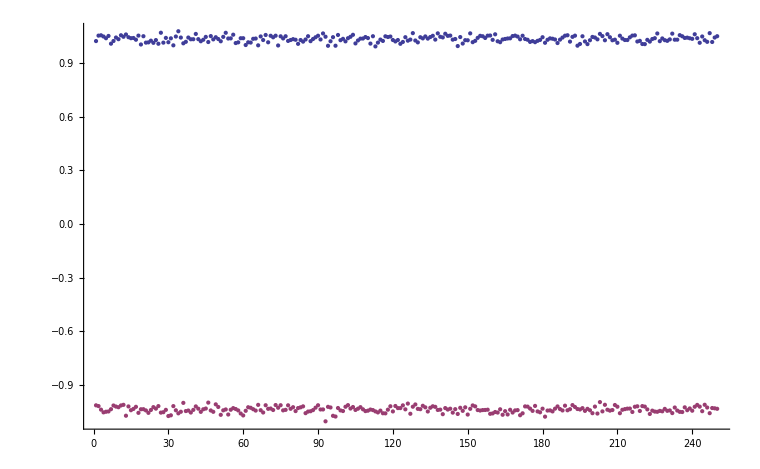

```mathematica
w=WeightVector[α,X,y];
b=Bias[α,X,y];
Length[X];
X[[SupportVectors[α]]]
yy=Map[w.##+b&,X,1];
xx=Map[w.##&,X,1];
(*DisplayTogether[ListPlot[w.X], ListPlot[Map[w.##+b&,X,1]]]*)
Show[ListPlot[{Extract[yy,Position[y,1]],Extract[yy,Position[y,-1]]}]]
(*SVMPlot[α,X,y]*)
```

```mathematica
testX=Join[tds,tdd];
testY={-1,1,1};
yy=Map[w.##+b&,testX,1]
```

{-1.99611,-4.83932,-1.19536}

```mathematica
ff[x_,y_,z_]:=w.{x,y,z}+b;
ContourPlot3D[ff[aa,bb,ee]==0,{aa,40,100},{bb,40,100},{ee,-10,1}]
```

Dot::dotsh: Tensors « 1 » and {40.00429`, 40.00429`, -9.9992135`} have incompatible shapes.

Dot::dotsh: Tensors « 1 » and {44.29000428571428`, 40.00429`, -9.9992135`} have incompatible shapes.

General::stop: Further output of Dot will be suppressed during this calculation.

ContourPlot3D::valuef: ff[aa, bb, ee] - 0 must be a numerical function.

ContourPlot3D[ff[aa,bb,ee]==0,{aa,40,100},{bb,40,100},{ee,-10,1}]

```mathematica
(*try something*)
xi=Join[expd,expd1]
xj=DeleteDuplicates[Tuples[expdd,2],(#1===#2||#1===RotateLeft[#2])&];
xj1=Map[Flatten,xj,1];
Length[xj1]
```

{89.9937,44.1168,0.801083,100.131,50.4274,0.748483}

36

```mathematica
Map[w.##+b&,xj1,1]
```

{1.26181,1.12516,1.04732,1.55018,1.60419,1.47307,1.0203,2.28744,1.28539,1.20755,1.71041,1.76442,1.6333,1.18053,2.44767,1.34221,1.84507,1.89908,1.76796,1.31519,2.58233,1.28058,1.33459,1.20347,0.7507,2.01784,1.29342,1.16231,0.709534,1.97667,1.2987,0.84593,2.11307,1.39484,2.66198,1.46628}

```mathematica
z=w.x;
f[z_]:=z+b;
∑_(j=1)^Length[X] (f[w.X[[j]]]-y[[j]])
```

7.96694

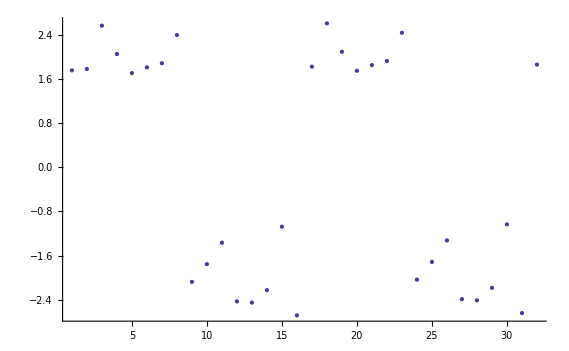

Dot::dotsh: Tensors {-0.21291221905107527`, -0.48495645034991863`, -0.01127680926122919`, « 20 », 0.36977706814458156`, 0.012502896567078217`} and {89.99372162941316`, 44.11683661468369`, 0.8010827713133797`} have incompatible shapes.

7.26252+{-0.212912,-0.484956,-0.0112768,0.209154,0.369777,0.0125029}.{89.9937,44.1168,0.801083}

```mathematica
ListPlot[Table[f[w.X[[j]]],{j,1,32}]]

f[w.Mean[pr]]
```

### aaa

```mathematica
{{1},{2},{3}}.{{1,1,1}}
```

{{1,1,1},{2,2,2},{3,3,3}}

```mathematica
Input["hello"]
```

aa

```mathematica
Remove[bb]
bb["nnn"]=11;
bb["str"]="aaa";
bb[kk]=IdentityKernel;
```

```mathematica
bb["nnn"]
```

11

```mathematica
Export["..\\tmp\\tt.mx",bb]
```

..\tmp\tt.mx

```mathematica
cc=Import["..\\tmp\\tt.mx"]
```

bb

```mathematica
Context[cc[kk]]
```

Context::ssle: Symbol, string, or HoldPattern[symbol] expected at position 1 in Context[cc[kk]].

Context[cc[kk]]

```mathematica
Context[kernel]
```

W`SVM`

```mathematica
Remove[f]
```

```mathematica
m={{1,2},{2,3}};
f[x_]:=Map[IdentityKernel[#,x]&,m];
```

```mathematica
f[{1,2}]
```

{5,8}

```mathematica
m[[1;;1]]
```

{{1,2}}

```mathematica
Total[Outer[IdentityKernel,m,m⟦{1}⟧,1]]//Flatten
```

{13}

```mathematica
Options[SVMTrain]
```

{svmType→1,kernelType→1,qpType→1,t→0.001,γ→1/3,degree→3,coef0→0}

```mathematica
OptionValue[SVMTrain]
```

OptionValue::optnf: Option name All not found in defaults for SVMTrain.

All

```mathematica
Options[expp]={a->1,b->2,c->"hello"};
```

```mathematica
Options[expp][[2]]
```

b→2

```mathematica
opt={a->2,b->10};
```

```mathematica
abc=Union[opt,Options[expp]]
```

{a→1,a→2,b→2,b→10,c→hello}

```mathematica
bb["opt"]:=opt
```

```mathematica
bb["opt"]
```

{a→2,b→10}

```mathematica
bb["opt"]={a,b}/.{opt}
```

{{2,10}}

```mathematica
bb["opt"]={svmType,kernelType,qpType,t,γ,degree,coef0}/.opt/.Options[SVMTrain]
```

{1,1,1,0.001,1/3,3,0}

```mathematica
bb["opt"]
```

{{1,1,1,0.001,1/3,3,0}}

```mathematica
{a,b}*{c,d}
```

{a c,b d}

```mathematica
ma=Table[i,{i,100000}];
mb=Table[i*i,{i,100000}];
Total[ma*mb]//Timing
ma.mb//Timing
```

{0.094,25000500002500000000}

{0.031,25000500002500000000}

```mathematica
C
```

C

### c-svm test

```mathematica
(*non-separable*)
dim=3;
mu1=Table[i,{i,dim}];
mu2=Table[-i,{i,dim}];
sgm=DiagonalMatrix[Table[5,{i,dim}]];
s1=RandomVariate[MultinormalDistribution[mu1,sgm],50];
s2=RandomVariate[MultinormalDistribution[mu2,sgm],50];

sample=Join[s1,s2];
Dimensions[sample]
ListPointPlot3D[{s1,s2},PlotStyle->{PointSize[Large]}]
```

{100,3}

-Graphics3D-

```mathematica
X=sample;
Y=Join[Table[1,{50}],Table[-1,{50}]];
Dimensions[X]
Dimensions[Y]
```

{100,3}

{100}

```mathematica
lm=SVMTrain[X,Y,svmType->2,qpType->2]
```

W`SVM`PP`svm$4051

```mathematica
Count[SVMClassify[lm,X][[2]]-Y,0]/Length[Y]
```

24/25

```mathematica
k=0.15;
```

```mathematica
m=SVMTrain[X,Y,svmType->3,nu->k];
```

```mathematica
Count[m["alpha"],0]
```

83

```mathematica
m["offset"]
```

-3.09181

```mathematica
SVMPlot[m,X]
```

-Graphics3D-

```mathematica
Count[SVMClassify[m,X][[2]]-Y,0]/Length[Y]
```

47/100

```mathematica
r=N[Reap[For[i=0.15,i< 1,i=i+0.005,
Sow[1-Count[ SVMClassify[SVMTrain[X,Y,svmType->3,nu->i],X][[2]]-Y,0]/Length[Y]];]][[2,1]]];
```

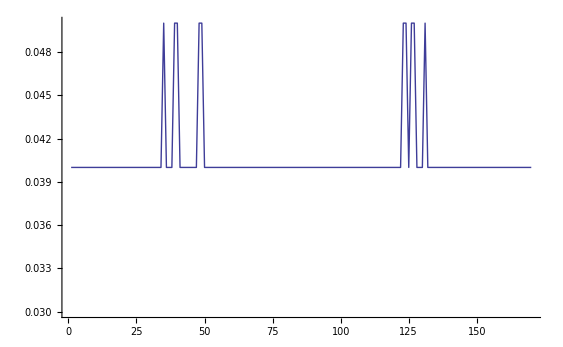

```mathematica
ListPlot[r,PlotRange->{0.03,0.05},Joined->True]
```